# twenty-fours

Michael Stern
April 18, 2016

The game of 24s can be perfectly solved using algebraic programming, provided only binary operators are allowed. Four cards picked, ten possibilties for each. This means ten thousand possible hands, or only 715 if we eliminate all redundant hands that can be rearranged to equal each other.

I am allowing addition, multiplication, subtraction, division, powers, roots, and logarithm but the code is general enough that this can be easily changed.

A normal user can go directly to the “run the code” section. It will execute the functions it needs from the other parts of the notebook.

## setup

```mathematica
allPossibleHandsUnsorted=Tuples[Range[10],4];
allPossibleHandsSorted1=Union[Sort/@allPossibleHandsUnsorted];
```

```mathematica
{Length[allPossibleHandsUnsorted],Length[allPossibleHandsSorted1]}
```

{10000,715}

## algebraic programming

### utility code

```mathematica
ReplaceAllList[expr_,rules_]:=Module[{i},Join[ReplaceList[expr,rules],If[AtomQ[expr],{},Join@@Table[ReplacePart[expr,#,i]&/@ReplaceAllList[expr[[i]],rules],{i,Length[expr]}]]]]
```

### algebraic programming

We have a choice -- make our function set commutative, so that {3,2} is processed as both 3-2 and 2-3, or make our card set comprehensive, so that both arrangements are passed through the function. I elected the latter, but the former should work equally well.

#### steps

Start by finding all the ways of associating four elements.

```mathematica
ClearAll[f];SetAttributes[f,{Flat,OneIdentity}];rawFunctions=Union[FixedPoint[Union[Flatten[ReplaceAllList[#,f[a_,b_]->g[a,b]]]]&,f[a,b,c,d]]/.f->g];
```

Then we remove all duplicates and expressions that involve the application of g to three elements.

```mathematica
uniqueFunctions=DeleteCases[rawFunctions,_?(Not[FreeQ[#,g[x__/;Length[{x}]≥3]]]&),1];
```

Finally we replace g by A_2,A_1,A_0, in this order, and swap in the numbers from a hand of cards

```mathematica
functionsWNumbers[hands_List]:=Map[(i=0;MapAll[If[#===g,#/.g->Subscript[A,Mod[++i,3]],#]&,uniqueFunctions,Heads->True]/.{a->#[[1]],b->#[[2]],c->#[[3]],d->#[[4]]})&,hands]
```

The screening step. I redefine some mathematica functions to limit their inputs and simplify the errors they output in the case of, for example, division by zero. This is intended to speed up processing and reduce memory requirements. It is not otherwise necessary, and it is possible that I am eliminating good solutions here. For example,  I prevent Log from returning imaginary solutions. This may be a bad decision, as some oddball 24s may be found by multiplying two imaginary numbers together. Expanding the input band on power and root to 25 does not yield additional solutions. When I have time, I’ll weaken or remove these constraints further and see if anything additional turns up.

```mathematica
Off[General::"spell1"];Off[General::"spell"];
power[x_?(#>0&),y_?(-16≤#≤16&)]:=x^y;power[x__]:=Indeterminate;
surd[x_Integer?(#>0&),y_Integer?(-16≤#≤16&&#≠0&)]:=Surd[x,y];
surd[x__]:=Indeterminate;
divide[x_,y_]/;y≠0:=Divide[x,y];divide[x_,0]:=Indeterminate;
log[x_?(#>0&),y_?(#>0&)]:=Log[x,y];log[x__]:=Indeterminate;
mod[x_Integer?(#>0&),y_Integer?(-16≤#≤16&&#≠0&)]:=Mod[x,y];
mod[x__]:=Indeterminate;
```

The following step generates every possible combination of operators. For six binary functions, we get 46,646 raw rules but only 216 rules once we constrict it down to four cards and eliminate redundancies. For seven binary functions, 823,543 rules, of which 343 are relevant to the game of 24s.

```mathematica
generateRules[binaryFunctions_List,numCards_Integer]:=Module[{raw,refined,numFuncs},
numFuncs=Length[binaryFunctions];
raw=ParallelMap[Thread,Map[RuleDelayed[Array[Subscript[A, #-1]&,{numFuncs}], #] &,Distribute[Array[binaryFunctions&,{numFuncs}],List]]];
(*In fact,since an actual hand never involves more than three binary operations,we remove the rules involving unnecessaryAs.*)
refined=Union[DeleteCases[raw,Apply[Alternatives,Map[HoldPattern[#]&,ParallelTable[Subscript[A, i]:>_,{i,numCards-1,numFuncs-1}]]],Infinity]];
refined
]
```

Now we map our selected functions over the generic rules from the previous step.

```mathematica
generateHands[functions_List,rules_List]:=Table[Union[#/.rules]&/@functions[[i]],{i,1,Length[functions]}]
```

When we get our answers, {1,1,2,2} is treated as distinct from {2,2,1,1}. Let’s fix that. The following assumes the cardSet is a single list of four integers {1,1,2,3}, and that the possibilitySet is a list of {{ordered four cards},{solutions}} like 
{{6,6,6,6},{((6+6)+6)+6,(6+(6+6))+6,(6+6)+(6+6),6+((6+6)+6),6+(6+(6+6)),6 6-(6+6),(6 6-6)-6}}

```mathematica
solutionsForSet[cardSet_List,possibilitySet_List]:=Module[{allVarieties,matches},
allVarieties=Permutations[cardSet];
matches=Select[possibilitySet,MemberQ[allVarieties,#[[1]]]&];
Flatten[matches[[All,2]],1]
]
```

#### all together now

```mathematica
legitCombos[hands_List,rules_List,allPossibleHandsSorted_List]:=Module[{functionsWithNumbers,everythingGeneratedFromTheseHands,patterns,allSolns},
functionsWithNumbers=
functionsWNumbers[hands];
everythingGeneratedFromTheseHands=generateHands[functionsWithNumbers,rules];
(* now find all the combinations that equal 24. This is the slow step *)
patterns=Table[Union[Flatten[Union[Flatten[Union[HoldForm[#]/.rules]]]&/@functionsWithNumbers[[i]]]],{i,1,Length[functionsWithNumbers]}];
(* print it out, replacing our constrained versions of the selected functions with Mathematica's native versions for pretty output *)
allSolns=Table[{hands[[i]],Select[patterns[[i]],ReleaseHold[#]==24&]},{i,1,Length[functionsWithNumbers]}]/.{surd->Surd,log->Log,mod->Mod,divide->Divide,max->Max,min->Min,power->Power};
Map[{#,solutionsForSet[#,allSolns]}&,allPossibleHandsSorted]
]
```

Given an answer list in the format discussed above, and a hand in list form, return all solutions pertaining to that hand.

```mathematica
getAnswers[hand_List,solutions_List]:=Select[solutions,#[[1]]==Sort[hand]&][[1]]/.{surd->Surd,log->Log,mod->Mod,divide->Divide,max->Max,min->Min,power->Power};
```

## run the code

If the screening step is done perfectly, it may be possible to skip the following line, which suppresses error reports on division by zero and the like.

```mathematica
Off[Divide::indet];
Off[Power::infy];
Off[Greater::nord];
Off[Infinity::indet];
Off[N::meprec];
Off[LessEqual::nord];
Off[General::ovfl];
```

```mathematica
(*rules=generateRules[{Times, Plus,Subtract,divide,power,surd,log,mod},4];*)
rules=generateRules[{Times, Plus,Subtract,divide},4];
```

```mathematica
Length[rules]
```

64

```mathematica
AbsoluteTiming[sortedPossibilities=legitCombos[allPossibleHandsUnsorted,rules,allPossibleHandsSorted1];] (* this is the slow step *)
```

{145.917,Null}

```mathematica
On[Divide::indet];
On[Power::infy];
On[Greater::nord];
On[Infinity::indet];
On[N::meprec];
On[LessEqual::nord];
On[General::ovfl];
```

With four operators, 64 possible combinations of rules. Absolute timing 148 seconds, or 190 if parallelized.
With five operators, 125 possible combinations of rules. Absolute timing  262 seconds.
With six operators, 216 combinations of rules. Absolute timing, 611 seconds
With eight operators, 512 combinations of rules. Absolute timing, 1940 seconds

## save data for twitter bot

### prep answer list in .mx format

Either (1) this should be done on the same OS/processor that will be running the bot so that the .mx binary is compatible, or (2) you need to run a converter after saving it.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"24s arithmetic.mx"}],sortedPossibilities];
```

```mathematica
answersArithmetic=Import[FileNameJoin[{NotebookDirectory[],"24s-arithmetic.mx"}]];
answersFancyOnly=Import[FileNameJoin[{NotebookDirectory[],"24s fancy only.mx"}]];
```

```mathematica
(* make fancy-only solutions *)
answersFancyOnly=MapThread[{#1[[1]],Complement[#2[[2]],#1[[2]]]}&,{answersArithmetic,answersFancy}];
Export[FileNameJoin[{NotebookDirectory[],"fours fancy only.mx"}],answersFancyOnly];
```

```mathematica
getAnswers[{8,9,1,1},answersArithmetic]
```

{{1,1,8,9},{}}

```mathematica
getAnswers[{8,9,1,1},answersFancy]
```

{{1,1,8,9},{9^(1/(1+1)) 8,8 9^(1/(1+1))}}

### save pix for bot

```mathematica
Remove[namifier]
```

```mathematica
Options[namifier]={"index to add"->False,"suffix"->".png"};
namifier[cards_List,OptionsPattern[]]:=Module[{sc,a,b,c,d},sc=Sort[cards];a=ToString[sc[[1]]];b=ToString[sc[[2]]];c=ToString[sc[[3]]];d=ToString[sc[[4]]];If[StringLength[a]==1,"0"<>a,a]<>If[StringLength[b]==1,"0"<>b,b]<>If[StringLength[c]==1,"0"<>c,c]<>If[StringLength[d]==1,"0"<>d,d]]<>If[IntegerQ[OptionValue["index to add"]],"-"<>ToString[OptionValue["index to add"]],""]<>OptionValue["suffix"];
```

```mathematica
Map[If[Length[#[[2]]]>0,Table[Export[(*filename*)FileNameJoin[{NotebookDirectory[],(*"24s-simple"*)"24s-fancy-only",namifier[#[[1]],"index to add"->i]}],(*pix*)Style[getAnswers[#[[1]],(*answersFancy*)answersFancyOnly][[2,i]],FontSize->24]],{i,1,Min[Length[#[[2]]],5(*max number of solutions to save in picture form*)]}]]&,(*answersFancy*)answersFancyOnly];
```

```mathematica
Options[showAnswer]={"noisy"->False,"output"->Length,"pixNo"->Automatic};
showAnswer[combo_List,whichPath_String,OptionsPattern[]]:=Module[{path,regex,namen,pixpath},
SetDirectory[];
path=Switch[whichPath,"simple",FileNameJoin[{NotebookDirectory[],"24s-arithmetic"}],"fancy",FileNameJoin[{NotebookDirectory[],"24s-fancy"}]];
If[OptionValue["noisy"],Print["path: ",path]];
SetDirectory[path];
regex=namifier[Sort[combo],"suffix"->""];
If[OptionValue["noisy"],Print["regex: ",regex]];
namen=FileNames[regex<>"*"];
If[OptionValue["noisy"],Print["namen: ",namen]];
Switch[OptionValue["output"],Length,Length[namen],"file names",namen,"one pix",pixpath=FileNameJoin[{path,regex<>"-"<>ToString[RandomInteger[{1,Length[namen]}]]<>".png"}];If[Length[namen]>0,If[OptionValue["noisy"],Print["pixpath: ",pixpath]];Import[pixpath]],_,"I dunno what '"<>OptionValue["output"]<>"' is."
]
]
```

```mathematica
showAnswer[{8,9,1,1},"fancy","noisy"->False,"output"->"one pix"]
```

-Graphics-

## analysis

#### solvable hands

715 hands. 566 can be solved with just arithmetics, 595 if we add roots, powers, and logs. 619 with Mod.

#### unsolveable hands

```mathematica
unsolvableHands=Select[sortedPossibilities,Length[#[[2]]]==0&][[All,1]]
```

{{1,1,1,1},{1,1,1,2},{1,1,1,3},{1,1,1,4},{1,1,1,6},{1,1,1,7},{1,1,1,9},{1,1,1,10},{1,1,2,2},{1,1,2,3},{1,1,5,9},{1,1,5,10},{1,1,6,7},{1,1,6,10},{1,1,7,7},{1,1,7,8},{1,1,7,9},{1,1,8,10},{1,1,9,9},{1,1,9,10},{1,1,10,10},{1,2,2,2},{1,2,9,10},{1,2,10,10},{1,4,9,9},{1,5,7,7},{1,6,6,7},{1,6,7,7},{1,6,7,8},{1,6,10,10},{1,7,7,7},{1,7,7,8},{1,7,10,10},{1,8,9,9},{1,8,9,10},{1,8,10,10},{1,9,9,9},{1,9,9,10},{1,9,10,10},{1,10,10,10},{2,2,2,2},{2,2,7,9},{2,6,7,7},{2,7,7,7},{2,7,7,9},{2,7,9,9},{2,9,9,9},{2,9,9,10},{2,10,10,10},{3,3,10,10},{3,5,7,7},{3,10,10,10},{4,4,9,9},{4,7,7,9},{4,7,7,10},{4,9,9,9},{5,5,5,7},{5,5,5,8},{5,5,5,10},{5,5,6,10},{5,5,7,9},{5,7,7,7},{5,7,9,9},{5,8,10,10},{5,9,9,9},{5,10,10,10},{6,6,6,7},{6,6,7,7},{6,6,7,8},{6,7,7,7},{6,7,7,8},{6,9,10,10},{7,7,7,7},{7,7,7,8},{7,7,7,9},{7,7,7,10},{7,7,8,8},{7,7,8,9},{7,7,9,9},{7,8,8,8},{7,9,9,9},{7,9,9,10},{7,9,10,10},{7,10,10,10},{8,8,8,8},{8,8,9,9},{8,8,10,10},{8,9,9,9},{8,9,9,10},{8,9,10,10},{8,10,10,10},{9,9,9,9},{9,9,9,10},{9,9,10,10},{9,10,10,10},{10,10,10,10}}

```mathematica
Length[unsolvableHands]/Length[allPossibleHandsSorted]//N
```

0.134266

So about 17% are unsolvable,  83% are solvable.

```mathematica
Length[allPossibleHandsSorted]-Length[unsolvableHands]
```

619

#### unique solutions

```mathematica
solvableHands=Select[sortedPossibilities,Length[#[[2]]]>0&];
```

```mathematica
uniqueSolutions=Select[solvableHands,Length[#[[2]]]==2&]
```

{{{1,1,2,4},{(1+4)^2-1,(4+1)^2-1}},{{1,1,3,3},{(1+1)^3 3,3 (1+1)^3}},{{1,1,8,9},{8 root[9,1+1],root[9,1+1] 8}},{{1,2,9,9},{(9-1) root[9,2],root[9,2] (9-1)}},{{1,6,6,6},{(6-1) 6-6,6 (6-1)-6}},{{2,5,5,10},{(5-2/10) 5,5 (5-2/10)}},{{3,3,3,3},{(3 3) 3-3,3 (3 3)-3}},{{3,5,10,10},{3 (10-10/5),(10-10/5) 3}},{{5,5,5,5},{5 5-5/5,5 5-Log[5,5]}},{{5,5,9,9},{5 5-9/9,5 5-Log[9,9]}},{{5,5,10,10},{5 5-10/10,5 5-Log[10,10]}},{{5,6,7,10},{6 mod[7^10,5],mod[7^10,5] 6}},{{5,7,7,8},{mod[7^7,5] 8,8 mod[7^7,5]}},{{5,8,9,9},{8 mod[9+9,5],mod[9+9,5] 8}},{{6,6,9,9},{6^mod[9,6]/9,6^(9-6)/9}},{{6,7,7,9},{6 mod[7 7,9],mod[7 7,9] 6}},{{6,7,9,10},{6^mod[10,7]/9,6^(10-7)/9}}}

Hands that can be solved with Mod but not without:

```mathematica
{5 5-mod[10,3]}
```

```mathematica
{5,6,7,10},6 mod[7^10,5]
{5,7,7,8},mod[7^7,5] 8
```

```mathematica
{6,7,7,9},{6 mod[7 7,9]
```

```mathematica
Mod[7^10,5]
```

4

#### easiest to solve

```mathematica
mostSolutions=Length[First[Sort[solvableHands,Length[#1[[2]]]>Length[#2[[2]]]&]][[2]]]
```

522

```mathematica
Select[solvableHands,Length[#[[2]]]==mostSolutions&][[All,1]]
```

{{1,1,3,8},{1,1,4,6}}

There are two hands — {1,1,3,8} and {1,1,4,6} that each have 522 solutions by the standards given. These are by this test the easiest hands in the game.

#### graph of number of solutions by hand

```mathematica
solutionsByHand=Table[{i,Length[sortedPossibilities[[i]][[2]]]},{i,1,Length[sortedPossibilities]}];
```

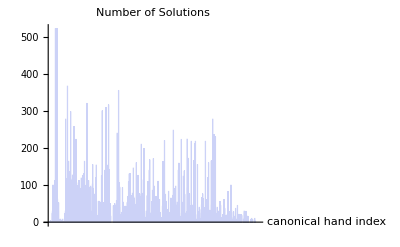

```mathematica
BarChart[solutionsByHand[[All,2]],PerformanceGoal->"Speed",BarSpacing->None,PlotLabel->"Number of Solutions",AxesLabel->{"canonical\nhand index",None}]
```

#### histogram by number of hands with each count of solutions

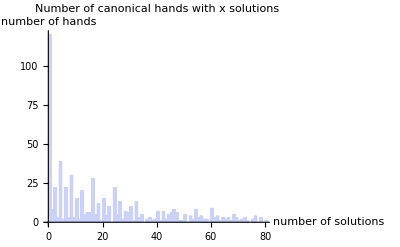

```mathematica
Histogram[solutionsByHand[[All,2]],500,PerformanceGoal->"Speed",PlotRange->{{0,80},Automatic},PlotLabel->"Number of canonical hands with x solutions",AxesLabel->{"number of\nsolutions","number\nof hands"},AxesOrigin->{0,0}]
```

## notes & to-do

The code should run much more quickly if rewritten to take advantage of multiple cores.